Шаг h

1

(0
1
2
3
4
5
6) (0.321513
0.847855
2.13629
2.10102
0.999991
0.286505
0.0497871)

2.13629

8.

Количество узлов

10

Степень многочлена 2

Шаг h

3/5

(0.
0.6
1.2
1.8
2.4
3.
3.6
4.2
4.8
5.4
6.) (0.321513
0.564545
1.05291
1.87865
2.40318
2.10102
1.43302
0.810583
0.382893
0.151072
0.0497871)

многочлен 1ого порядка:

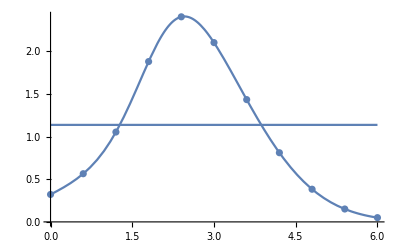

6.99858

многочлен 2ого порядка:

{-0.172647,0.862635,0.661115}

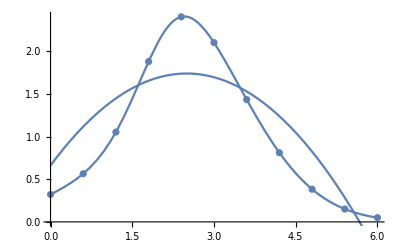

1.82291

Многочлен 4ого порядка:

{{0.,0.321513},{0.6,0.564545},{1.2,1.05291},{1.8,1.87865},{2.4,2.40318},{3.,2.10102},{3.6,1.43302},{4.2,0.810583},{4.8,0.382893},{5.4,0.151072},{6.,0.0497871}}

General::ivar: 2. is not a valid variable.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

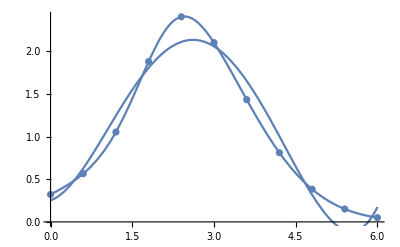

0.306161

Многочлен 5ого порядка:

{{0.,0.321513},{0.6,0.564545},{1.2,1.05291},{1.8,1.87865},{2.4,2.40318},{3.,2.10102},{3.6,1.43302},{4.2,0.810583},{4.8,0.382893},{5.4,0.151072},{6.,0.0497871}}

General::ivar: 2. is not a valid variable.

ReplaceAll::reps: {FindFit[{{0.,0.321513},{0.6,0.564545},{1.2,1.05291},{1.8,1.87865},{2.4,2.40318},{3.,2.10102},{3.6,1.43302},{4.2,0.810583},{4.8,0.382893},{5.4,0.151072},«1»},8. e+«4»+16. w,{«1»},2.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

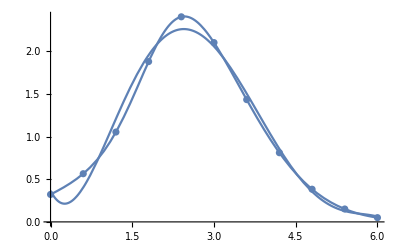

0.0892385

```mathematica
a = 0;b=6;n =6;
"Шаг h" 
 h=(b-a)/n
f[x_]:=(Exp[x-x^2/4]*Tanh[x^3/11+1/3]);
XDT={};YDT={};
For[i=0,i<=n,i++,
xdata[i] = a+i×h;
ydata[i]=N[f[xdata[i]]];
XDT = Append[XDT,xdata[i]];
YDT= Append[YDT, ydata[i]];
];
Array[xdata,n+1,0];Array[ydata,n+1,0];
MatrixForm[XDT]   MatrixForm[YDT]
For[i=0,i<=n,i++,xdata[i]=XDT[[i+1]];ydata[i]=YDT[[i+1]];];
pln=∑_(i=0)^n ydata[i]*∏_(j=0)^n If[i!=j,(x-xdata[j])/(xdata[i]-xdata[j]),1];
lgr2[x_]:=Collect[pln,x];
lgr2[x]
"8."
"Количество узлов"
n = 10
"Степень многочлена 2"
"Шаг h"
h = (b-a)/n
XDT = {}; YDT ={};
For[i=0,i<=n,i++,
xdata[i] = N[a+i×h];
ydata[i]=N[f[xdata[i]]];
XDT = Append[XDT,xdata[i]];
YDT= Append[YDT, ydata[i]];
];
Array[xdata,{n+1,0}];
Array[ydata,{n+1,0}];
MatrixForm[XDT]   MatrixForm[YDT]
"многочлен 1ого порядка:"
ex = ∑_(i=0)^n xdata[i];ey=∑_(i=0)^n ydata[i];
exx=∑_(i=0)^n xdata[i]^2;eyy=∑_(i=0)^n ydata[i]^2;exy=∑_(i=0)^n xdata[i]*ydata[i];
l=(ey*exx-ex*exy)/((n+1)*exx-ex^2);
m=((n+1)*exy-ex*ey)/((n+1)*exx-ex^2);
p[x_]=l+m*x;
gr1:=Plot[f[x],{x,a,b}];
gr2:=ListPlot[Table[{N[xdata[i]],N[ydata[i]]},{i,a,10}]];
gr3:=Plot[p[x],{x,a,b}];
Show[gr1,gr2,gr3]
sumq=0;
For[i=0,i<=n,i++,
sumq=sumq+Abs[p[xdata[i]]-f[xdata[i]]]^2;]
Print[sumq];
"многочлен 2ого порядка:"
A={{∑_(i=0)^n xdata[i]^4,∑_(i=0)^n xdata[i]^3,∑_(i=0)^n xdata[i]^2},{∑_(i=0)^n xdata[i]^3,∑_(i=0)^n xdata[i]^2,∑_(i=0)^n xdata[i]},{∑_(i=0)^n xdata[i]^2,∑_(i=0)^n xdata[i],n}};
B={∑_(i=0)^n xdata[i]^2*ydata[i],∑_(i=0)^n xdata[i]*ydata[i],∑_(i=0)^n ydata[i]};
LinearSolve[A,B]
p[x_]:=-0.17264732708012134 x^2+0.8626347972245298x+0.6611149510344284;
gr1:=Plot[f[x],{x,a,b}];
gr2:=ListPlot[Table[{N[xdata[i]],N[ydata[i]]},{i,a,10}]];
gr3:=Plot[p[x],{x,a,b}];
Show[gr1,gr2,gr3]
sumq=0;
For[i=0,i<=n,i++,
sumq=sumq+Abs[p[xdata[i]]-f[xdata[i]]]^2;]
Print[sumq];
"Многочлен 4ого порядка: "
data=Table[{N[xdata[i]],N[ydata[i]]},{i,0,n}]
rules=FindFit[data,q*x^4+w*x^3+e*x^2+r*x+t,{q,w,e,r,t},x];
y=q*x^4+w*x^3+e*x^2+r*x+t/.rules;
p[x_]:=0.2530945139119096+0.209524689868782 x+0.8882660162815582 x^2-0.3509195423043966 x^3+0.032781858896235756 x^4;
gr1:=Plot[f[x],{x,a,b}];
gr2:=ListPlot[Table[{N[xdata[i]],N[ydata[i]]},{i,a,10}]];
gr3:=Plot[p[x],{x,a,b}];
Show[gr1,gr2,gr3]
sumq=0;
For[i=0,i<=n,i++,
sumq=sumq+Abs[p[xdata[i]]-f[xdata[i]]]^2;]
Print[sumq];
"Многочлен 5ого порядка: "
Clear[q,w,e,r,t,o]
data=Table[{N[xdata[i]],N[ydata[i]]},{i,0,n}]
rules=FindFit[data,q*x^5+w*x^4+e*x^3+r*x^2+t*x+o,{q,w,e,r,t,o},x];
y=q*x^5+w*x^4+e*x^3+r*x^2+t*x+o/.rules;
p[x_]:=0.36496391160581615-1.2520282744469633 x+2.895182294355102 x^2-1.2932350707188531 x^3+0.21261306660891766 x^4-0.011988747180845432 x^5;
gr1:=Plot[f[x],{x,a,b}];
gr2:=ListPlot[Table[{N[xdata[i]],N[ydata[i]]},{i,a,10}]];
gr3:=Plot[p[x],{x,a,b}];
Show[gr1,gr2,gr3]
sumq=0;
For[i=0,i<=n,i++,
sumq=sumq+Abs[p[xdata[i]]-f[xdata[i]]]^2;]
Print[sumq];
```